```mathematica
hzeta[n_,s_,y_]:=Sum[ j^-s,{j,y,n}]-s/(1-s) n (Sum[ j^(-s-1),{j,1,Infinity}]-Sum[j^(-s-1),{j,1,y+n}])
hzeta2[n_,s_,y_]:=Sum[ j^-s,{j,y,n}]-s/(1-s) n (Sum[ j^(-s-1),{j,y+n,Infinity}])
```

```mathematica
hzeta2[1000000,.5,2]
```

-2.45835

```mathematica
Zeta[.5,2]
```

-2.46035

```mathematica
FullSimplify[(D[-x^(1-s) Sum[ (j+y)^-s,{j,0,n/x}],{x,1}]/.x->1)/(1-s)]
```

-HurwitzZeta[s,y]+HurwitzZeta[s,1+n+y]-(n s HurwitzZeta[1+s,1+n+y])/(-1+s)

```mathematica
FullSimplify[(D[-x^(1-s) Sum[ (j+y)^-s,{j,0,n/x}],{x,2}]/.x->1)/(1-s)/s]
```

((-1+s) HurwitzZeta[s,y]-(-1+s) HurwitzZeta[s,1+n+y]+n (2 s HurwitzZeta[1+s,1+n+y]-n (1+s) HurwitzZeta[2+s,1+n+y]))/(-1+s)

```mathematica
FullSimplify[(D[-x^(1-s) Sum[ (j+y)^-s,{j,0,n/x}],{x,3}]/.x->1)/(1-s)/s/(s+1)]
```

(-(-1+s) HurwitzZeta[s,y]+(-1+s) HurwitzZeta[s,1+n+y]+n (-3 s HurwitzZeta[1+s,1+n+y]+3 n (1+s) HurwitzZeta[2+s,1+n+y]-n^2 (2+s) HurwitzZeta[3+s,1+n+y]))/(-1+s)

```mathematica
FullSimplify[(D[-x^(1-s) Sum[ (j+y)^-s,{j,0,n/x}],{x,4}]/.x->1)/(1-s)/s/(s+1)/(s+2)]
```

((-1+s) HurwitzZeta[s,y]-(-1+s) HurwitzZeta[s,1+n+y]+n (4 s HurwitzZeta[1+s,1+n+y]-6 n (1+s) HurwitzZeta[2+s,1+n+y]+4 n^2 (2+s) HurwitzZeta[3+s,1+n+y]-n^3 (3+s) HurwitzZeta[4+s,1+n+y]))/(-1+s)

```mathematica
rs[n_,s_,y_,k_]:= Sum[ (-1)^j Binomial[k,j]((s-1+j)/(s-1))n^j  Zeta[s+j,y+n],{j,0,k}]
rst[n_,s_,y_,k_]:= Table[ (-1)^j Binomial[k,j]((s-1+j)/(s-1))n^j  Zeta[s+j,y+n],{j,0,k}]
rs2[n_,s_,y_,k_]:= Sum[j^-s,{j,y,n+y}]-Sum[ (-1)^j Binomial[k,j]((s-1+j)/(s-1))n^j  Zeta[s+j,y+n+1],{j,1,k}]
rs3[n_,s_,y_,k_]:= Sum[j^-s,{j,y,n+y-1}]-Sum[ (-1)^j Binomial[k,j]((s-1+j)/(s-1))n^j  Zeta[s+j,y+n],{j,1,k}]
rsa[n_,s_,y_,k_]:= Sum[ (-1)^j Binomial[k,j]((s-1+2j)/(s-1))n^(2j)  Zeta[s+2j,y+n],{j,0,k}]
rsat[n_,s_,y_,k_]:= Table[ (-1)^j Binomial[k,j]((s-1+2j)/(s-1))n^(2j)  Zeta[s+2j,y+n],{j,0,k}]
rsax[n_,s_,y_,k_,x_]:= Sum[ (-1)^j Binomial[k,j]((s-1+x j)/(s-1))n^(x j)  Zeta[s+x j,y+n],{j,0,k}]
rsat[n_,s_,y_,k_,x_]:=Table[ (-1)^j Binomial[k,j]((s-1+x j)/(s-1))n^(x j)  Zeta[s+x j,y+n],{j,0,k}]
(* !!!!!!!!!!!!!! *)
rsats[n_,s_,y_,k_,x_]:=Table[ (((s-1+x j)/(s-1))n^(x j)  Zeta[s+x j,y+n]),{j,0,k}]
```

```mathematica
Chop@rs[1000000,-.5,4,4]
```

4.76837×10^-7

```mathematica
N[Chop@rs3[10000,.5,1,2]]
```

-1.46035

```mathematica
N@Zeta[.5,1]
```

-1.46035

```mathematica
Chop@N@rsa[100000,.5+I,1,3]
```

0

```mathematica
Chop@N@rsat[10000000,.5+4I,1,4]//TableForm
```

-769.735+151.301 ⅈ
3078.94-605.205 ⅈ
-4618.41+907.808 ⅈ
3078.94-605.205 ⅈ
-769.735+151.301 ⅈ

```mathematica
Chop@N@rst[10000000,N[ZetaZero[1]],1,3]//TableForm
```

-222.581+21.1516 ⅈ
667.744-63.4549 ⅈ
-667.744+63.4549 ⅈ
222.581-21.1516 ⅈ

```mathematica
rsat[100000,1.5,1,7,5]//TableForm
```

0.00632454
-0.0442707
0.132809
-0.221342
0.221337
-0.132799
0.0442651
-0.00632343

```mathematica
rsats[1000000,.5,1,3,7]//TableForm
```

-2000.
-1999.99
-1999.99
-1999.98

```mathematica
rsats[1000000,N[ZetaZero[1]],0,1,2]//TableForm
```

-36.0507-60.8221 ⅈ
-36.0507-60.8222 ⅈ

```mathematica
rsatsa[n_,s_,x_]:=FullSimplify[Table[( m[-n^(j x)]) (-1+s+j x)( zetaa[s+x j,n]),{j,0,1}]]
rsatsb[n_,s_,x_]:=FullSimplify[Table[ -n^(j x) (-1+s+j x)( Zeta[s+x j,n]),{j,0,1}]]
rsatsc[n_,s_,x_]:=Sum[ (-1)^j (-n^(j x)) (-1+s+j x)( Zeta[s+x j,n]),{j,0,1}]
rsatsd[n_,s_,y_,x_]:=  (-n^y) (-1+s+y)( Zeta[s+y,n])- (-n^x) (-1+s+ x)( Zeta[s+x ,n])
rsatsda[n_,s_,y_,x_]:= { (-n^y) (-1+s+y)( Zeta[s+y,n]), (-n^x) (-1+s+ x)( Zeta[s+x ,n])}
rsatsda2[n_,s_,y_,x_]:=  ((-n^y) ( Zeta[s+y,n]))/( (-n^x)( Zeta[s+x ,n]))
```

```mathematica
rsatsa[n,N[ZetaZero[1]],0.+6.887314497036861 ⅈ]
```

{(-0.5+14.1347 ⅈ) m[-1.+0. ⅈ] zetaa[0.5+14.1347 ⅈ,n],(-0.5+21.022 ⅈ) m[-n^(0.+6.88731 ⅈ)] zetaa[0.5+21.022 ⅈ,n]}

```mathematica
N[1-2 ZetaZero[1]]
```

0.-28.2695 ⅈ

```mathematica
N[1- ZetaZero[1]]
```

0.5-14.1347 ⅈ

```mathematica
20^(-28.26945028346939 ⅈ)
```

-0.990861-0.134885 ⅈ

```mathematica
N[20^(1-2ZetaZero[1])]
```

-0.990861-0.134885 ⅈ

```mathematica
1-N[2ZetaZero[1]]
```

0.-28.2695 ⅈ

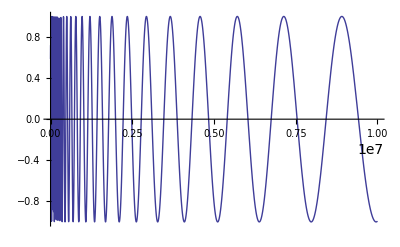

```mathematica
Plot[ Re[ x^(1-2ZetaZero[1])],{x,0,10000000}]
```

```mathematica
rsatsa[1000000000000,sos=N[ZetaZero[1]+.1],1-2sos]
```

{(-0.4+14.1347 ⅈ) m[-1.+0. ⅈ] zetaa[0.6+14.1347 ⅈ,1000000000000],(-0.6-14.1347 ⅈ) m[0.00165236+0.00362196 ⅈ] zetaa[0.4-14.1347 ⅈ,1000000000000]}

```mathematica
rsatsc[100000000000,sos=N[ZetaZero[1]+.1],1-2sos]
```

4.39337×10^-7-3.52503×10^-6 ⅈ

```mathematica
rsatsb[100000000000,sos=N[ZetaZero[1]+.1],1-2sos]
```

{-24903.4-3283.19 ⅈ,-24903.4-3283.19 ⅈ}

```mathematica
N[Zeta[ZetaZero[1]-.1]]
```

-0.0814815-0.013674 ⅈ

```mathematica
FullSimplify[(1-s)(((s-1+x j)/(s-1))n^(x j))]
```

-n^(j x) (-1+s+j x)

```mathematica
(-1)^j (-n^(j x)) (-1+s+j x)/.j->1
```

n^x (-1+s+x)

```mathematica
N[Zeta[s,n]/( n^x Zeta[s+x,n])/.s->11/.x->2/.n->1000000000000000]
```

1.2

```mathematica
N[1+(2/(11-1))]
```

1.2

```mathematica
rsatsd[100000000000,1+I,-.5,.5]
```

4.90563×10^-12-9.72444×10^-13 ⅈ

```mathematica
rsatsda[100000000000,1+I,-.2,.5]
```

{-0.980913+0.194448 ⅈ,-0.980913+0.194448 ⅈ}

```mathematica
n^y/n^x
```

n^(-x+y)

```mathematica
rsatsda2[1000000000000000,3,.3,.2]
```

0.956522

```mathematica
(3-1+.2)/(3-1+.3)
```

0.956522

```mathematica
N[ZetaZero[2]-ZetaZero[1]]
```

0.+6.88731 ⅈ

```mathematica
FullSimplify[(-1/2+x)/(-1/2-x)]/.x->14I
```

-783/785-(56 ⅈ)/785

```mathematica
N[n^(-2* 14I)/.n->10000000000000]
```

-0.78737-0.61648 ⅈ

```mathematica
N[1/5^(1/2+14I)]
```

-0.383353+0.230305 ⅈ

```mathematica
N[10000000^(14I)]
```

0.857023-0.515278 ⅈ

```mathematica
rsatsda[10,.5,-14I,14I]
```

{-2.54891+2.21912 ⅈ,-2.54891-2.21912 ⅈ}

```mathematica
N[(10^800)^(-(.1+23I))]
```

9.98887×10^-81-4.71673×10^-82 ⅈ

```mathematica
Sum[ 1/(j^(1/2-((.1+23I)))),{j,1,n}]
```

HarmonicNumber[n,0.4-23. ⅈ]

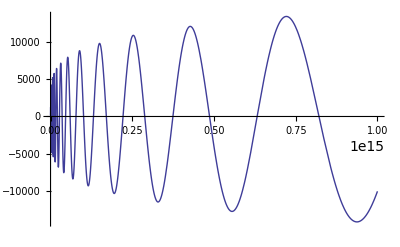

```mathematica
Plot[(Abs[(-.5-a)n^(-a)HarmonicNumber[n,.5-a]]-Abs[(-.5+a)n^(a)HarmonicNumber[n,.5+a]])/.a->(-.2+12I)/.b->(-.1+12I),{n,1,10^15}]
```

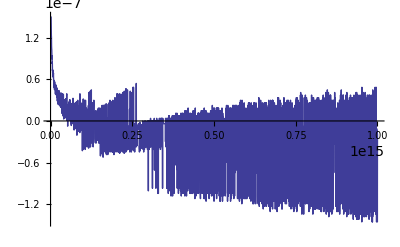

```mathematica
Plot[{Abs[(-.5-a)n^(-a)(Zeta[.5-a]-HarmonicNumber[n,.5-a])]-Abs[(-.5+a)n^(a)(Zeta[.5+a]-HarmonicNumber[n,.5+a])]}/.a->(.2+11I),{n,1,10^15}]
```

```mathematica
Expand[(-.5-a)n^(-a)j^-(.5-a)-(-.5+a)n^(a)j^-(.5+a)]
```

-0.5 j^(-0.5+a) n^-a-a j^(-0.5+a) n^-a+0.5 j^(-0.5-a) n^a-a j^(-0.5-a) n^a

```mathematica
N[(-1+s) Zeta[s,n]/.s->(1-.1^10)/.n->10^100]
```

1.

```mathematica
t2[x_,n_]:=x n^x Sum[ j^(-x-1),{j,1,n}]
t3[n_,s_]:=(s-1) n^(s-1) Sum[ j^(-s),{j,1,n}]
t3a[n_,s_]:={(s-1), n^(s-1), Sum[ j^(-s),{j,1,n}]}
```

```mathematica
t2[N@ZetaZero[1]-1,100000]
```

-1.+0.0000706736 ⅈ

```mathematica
t3[10000000000000000000000000,12.0]
```

1.10027×10^276

```mathematica
t3a[10000000000000000000,.1]
```

{-0.9,7.94328×10^-18,1.39881×10^17}

```mathematica
n^-x / n^x
```

n^(-2 x)

```mathematica
j^(1/2-x) j^x
```

√j

```mathematica
(j^x n^-x (1/2+x)-j^-x n^x (1/2-x))/j^(1/2)
```

(-j^-x n^x (1/2-x)+j^x n^-x (1/2+x))/(√j)

```mathematica
j^x/j^(1/2)
```

j^(-1/2+x)

```mathematica
tg[n_,x_]:= (-1/2 - x)n^-x (-Sum[ j^(-1/2+x),{j,1,n}]) - (-1/2 + x)n^x (-Sum[ j^(-1/2-x),{j,1,n}])
tg2[n_,x_]:= (1/2 + x)n^-x (Sum[ j^(-1/2+x),{j,1,n}]) - (1/2 - x)n^x (Sum[ j^(-1/2-x),{j,1,n}])
tg3[n_,x_]:=  (Sum[ (1/2 + x)n^-x j^(-1/2+x),{j,1,n}]) - (Sum[(1/2 - x)n^x  j^(-1/2-x),{j,1,n}])
tg4[n_,x_]:= Sum[ n^-x (1/2 + x)j^(-1/2+x)-n^x (1/2 - x) j^(-1/2-x),{j,1,n}]
tg4a[n_,x_,j_]:=  n^-x (1/2 + x)j^(-1/2+x)-n^x (1/2 - x) j^(-1/2-x)
```

```mathematica
N@tg4[100000000000000,21.022039638771556 ⅈ]
```

0.+2.7836×10^-6 ⅈ

```mathematica
FullSimplify[tg4[n,x]]
```

1/2 n^-x ((1+2 x) HarmonicNumber[n,1/2-x]+n^(2 x) (-1+2 x) HarmonicNumber[n,1/2+x])

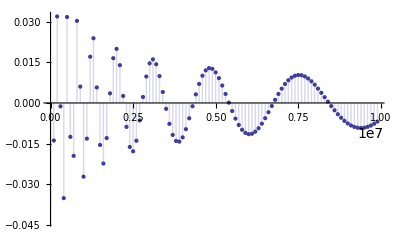

```mathematica
DiscretePlot[Im[ tg4a[1000000000,14.134725141734695 ⅈ,j]],{j,1,10000000,100000}]
```

```mathematica
D[tg4a[n,x,j],n]
```

-j^(-1/2-x) n^(-1+x) (1/2-x) x-j^(-1/2+x) n^(-1-x) x (1/2+x)

```mathematica
tg4b[n_,x_]:= Sum[ n^-x (1/2 + x)j^(-1/2+x)-n^x (1/2 - x) j^(-1/2-x),{j,1,Infinity}]-Sum[ n^-x (1/2 + x)j^(-1/2+x)-n^x (1/2 - x) j^(-1/2-x),{j,n+1,Infinity}]
```

```mathematica
N@tg4b[100000000000000,21.022039638771556 ⅈ]
```

$Aborted

```mathematica
FullSimplify[s n^(1-2s)/(1-s)]
```

(n^(1-2 s) s)/(1-s)

```mathematica
rsatsd[n_,s_,y_,x_]:=  (-n^y) (-1+s+y)( Zeta[s+y,n])- (-n^x) (-1+s+ x)( Zeta[s+x ,n])
```

```mathematica
sa1[n_,s_]:=Sum[ (-1)^(j+1) j^-s,{j,1,n}]
sa2[n_,s_]:=Sum[  j^-s,{j,1,n}]-(2^(1-s))Sum[  j^-s,{j,1,n/2}]
sa3[n_,s_,x_]:=Sum[  j^-s,{j,1,n}]-(x^(1-s))Sum[  j^-s,{j,1,n/x}]
```

```mathematica
N@sa2[100,2]
```

0.822418

```mathematica
D[sa3[n,s,x],x]/.x->1
```

-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
Table[(-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])/.s->-2),{n,1,10}]
```

{-5/6,-8/3,-11/2,-28/3,-85/6,-20,-161/6,-104/3,-87/2,-160/3}

```mathematica
Table[ -n(6n+4)/12,{n,1,10}]
```

{-5/6,-8/3,-11/2,-28/3,-85/6,-20,-161/6,-104/3,-87/2,-160/3}

```mathematica
Table[(-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])/.s->-1),{n,1,10}]
```

{-1/2,-1,-3/2,-2,-5/2,-3,-7/2,-4,-9/2,-5}

```mathematica
Table[ -n/2,{n,1,10}]
```

{-1/2,-1,-3/2,-2,-5/2,-3,-7/2,-4,-9/2,-5}

```mathematica
Table[(-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])/.s->-3),{n,1,10}]
```

{-1,-6,-18,-40,-75,-126,-196,-288,-405,-550}

```mathematica
Table[ -n^2(n+1)/2,{n,1,10}]
```

{-1,-6,-18,-40,-75,-126,-196,-288,-405,-550}

```mathematica
Table[((-(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])/.s->-4))30,{n,1,10}]
```

{-31,-392,-1743,-5104,-11855,-23736,-42847,-71648,-112959,-169960}

```mathematica
ark0[n_,s_,y_,x_]:=  (-n^y) (-1+s+y)( Zeta[s+y,n])- (-n^x) (-1+s+ x)( Zeta[s+x ,n])
ark[n_,s_,t_]:=   {(s-1)( n^s Zeta[s] - Sum[ (n/j)^s,{j,1,n}]),(t-1)( n^t Zeta[t] - Sum[ (n/j)^t,{j,1,n}])}
ark2[n_,s_,t_]:=   (s-1)( n^s Zeta[s,n])- (t-1)( n^t Zeta[t,n])
ark4[n_,y_,x_]:=  {(n^y) (-1+y)( Zeta[y,n]), (n^x) (-1+ x)( Zeta[x ,n])}
tes[n_,s_]:=   (s-1)( n^s Zeta[s] - Sum[ (n/j)^s,{j,1,n}])
tes2[n_,s_]:=   (s-1)n^s Zeta[s,n+1]
tesa[n_,s_]:=tes2[n,s]-n-(1-s)/2
tes4[n_,s_]:=   (s-1)n^(s-1) ( Zeta[s] - Sum[ (1/j)^s,{j,1,n}])
```

```mathematica
ark2[100000000000000000,.4+5I,.7]
```

-16.+4. ⅈ

```mathematica
ark[34567,3.3,1.73]
```

{34587.4,34566.6}

```mathematica
ark4[23456,3.3,1.73]
```

{23457.2,23456.4}

```mathematica
Table[{t, N[tes[scc=16000,t]-scc-(1-t)/2],N[tes2[scc=16000,t]-scc-(1-t)/2]},{t,-5,5,1/2}]//TableForm
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

-5 | 0.00015625 | 0.00015625
-9/2 | 0.000128906 | 0.000128906
-4 | 0.000104167 | 0.000104167
-7/2 | 0.0000820313 | 0.0000820312
-3 | 0.0000625 | 0.0000625
-5/2 | 0.0000455729 | 0.0000455729
-2 | 0.00003125 | 0.00003125
-3/2 | 0.0000195312 | 0.0000195313
-1 | 0.0000104167 | 0.0000104167
-1/2 | 3.90625×10^-6 | 3.90625×10^-6
0 | 0. | 0.
1/2 | -1.30208×10^-6 | -1.30208×10^-6
1 | Indeterminate | Indeterminate
3/2 | 3.90696×10^-6 | 3.90625×10^-6
2 | 0.0000103116 | 0.0000103663
5/2 | 0.000012435 | 0.0000195312
3 | 0. | 0.00003125
7/2 | -0.109787 | 0.0000455729
4 | -38.5 | 23.1587
9/2 | -2927.72 | 0.0000820312
5 | 1.03258×10^6 | 0.000104167

```mathematica
N[tes[1200,N[ZetaZero[1]]]]
```

1200.24-7.06736 ⅈ

```mathematica
Table[{t, N[tes4[scc=16000,t]]},{t,-5,5,1/2}]//TableForm
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

-5 | 1.00019
-9/2 | 1.00017
-4 | 1.00016
-7/2 | 1.00014
-3 | 1.00013
-5/2 | 1.00011
-2 | 1.00009
-3/2 | 1.00008
-1 | 1.00006
-1/2 | 1.00005
0 | 1.00003
1/2 | 1.00002
1 | Indeterminate
3/2 | 0.999984
2 | 0.999969
5/2 | 0.999953
3 | 0.999938
7/2 | 0.999921
4 | 1.00135
9/2 | 0.40265
5 | 0.